# Computational Analysis of the Time Dependent Schroedinger Equation

By: Andrew DeBenedictis, Anna Phillips, and Jen Radoff

## Introduction

## Importing Python-generated data

```mathematica
NotebookDirectory[]
```

C:\Users\a\Box Sync\Tufts\tims class\TDSE\GradStudentsRock_TDSE\

```mathematica
path=NotebookDirectory[];
cases={"freeParticle","harmonicOscillator"};
scheme={"","_CN"};
numberType={"Real","Imag"};
periodicType={"periodic","nonPeriodic"};
```

## Free Particle

### Scheme 1

this imports in form {rows, columns} equal to {time, position}

```mathematica
freeRe=Import[path<>"/Runs/"<>cases⟦1⟧<>"/"<>periodicType⟦1⟧<>scheme⟦1⟧<>"_"<>numberType⟦1⟧<>".csv","CSV"] ;
```

```mathematica
freeIm=Import[path<>"/Runs/"<>cases⟦1⟧<>"/"<>periodicType⟦1⟧<>scheme⟦1⟧<>"_"<>numberType⟦2⟧<>".csv","CSV"] ;
```

```mathematica
free=Sqrt[freeRe^2+freeIm^2];
```

```mathematica
Manipulate[ListPlot[{free⟦t,All⟧,freeRe⟦t,All⟧,freeIm⟦t,All⟧},PlotRange->{-.7,.7}],{t,1,Length[freeRe⟦All,1⟧],1}]
```

### Scheme 2

This should be the most stable scheme. For the rest of the cases, we will implement this scheme.

this imports in form {rows, columns} equal to {time, position}

```mathematica
freeNCRe=Import[path<>"/Runs/"<>cases⟦1⟧<>"/"<>periodicType⟦1⟧<>scheme⟦2⟧<>"_"<>numberType⟦1⟧<>".csv","CSV"] ;
```

```mathematica
freeNCIm=Import[path<>"/Runs/"<>cases⟦1⟧<>"/"<>periodicType⟦1⟧<>scheme⟦2⟧<>"_"<>numberType⟦2⟧<>".csv","CSV"] ;
```

```mathematica
freeNC=Sqrt[freeNCRe^2+freeNCIm^2];
```

```mathematica
Manipulate[ListPlot[{freeNC⟦t,All⟧,freeNCRe⟦t,All⟧,freeNCIm⟦t,All⟧},PlotRange->{-.7,.7}],{t,1,Length[freeNCRe⟦All,1⟧],1}]
```

#### compare the two schemes directly

```mathematica
Manipulate[ListPlot[{free⟦t,All⟧,freeNC⟦t,All⟧},PlotRange->{0,.7}],{t,1,Length[freeNCRe⟦All,1⟧],1}]
```

#### and check normalization

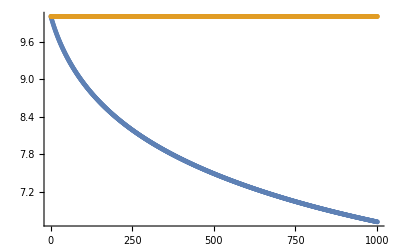

```mathematica
ListPlot[{Total[free^2,{2}],Total[freeNC^2,{2}]}]
```

Scheme 2 doesn’t lose normalization!

### Scheme 2 with non-Periodic boundary conditions

Weird things should happen here!

## Square Well

Non-periodic

## Harmonic Oscillator

Non-periodic

## Triangle

Non-periodic

## Kronig-Penney

Periodic

## Barrier

Non-periodic. Grid size is large compared to barrier width.

### Height = E

### Height < E

### Height > E

## V=ix

Non-periodic

## V=x+ix

Non-periodic

## Discussion?

About the non-Hermitian-ness...